# Math transformer for the AP-M1-CBS module

Just another code, based on the original toy code thingy.
Supposed to print out Yaml or so.

TODO: INT and SUM gatter need inverted output. MUL gatter needs proper scaling (/100).

```mathematica
ClearAll["Global`*"]
```

```mathematica
ComputationalParts={Summer,Multiplier,Integrator};
LogicLevels={PlusOne,MinusOne,UnconnectedInput};
HelperParts = { ReadoutVariable };
ElementaryParts =Join[ComputationalParts,LogicLevels,HelperParts];
devName = Symbol[ToString@#<>"Dev"]&; (* map part -> device name *)
undev=Symbol@StringTrim[ToString@#,"Dev"]&; (* map device -> part name *)
undevReplace=devName@#-> #&/@ElementaryParts; (* replace device -> part name *)
(* short names only for printing *)
shortSymbols={Summer -> Σ, Multiplier -> Π, Integrator-> "∫",
PlusOne-> 𝟙,MinusOne-> -𝟙,UnconnectedInput-> ∅};
(*shortName =#//.Join[shortSymbols,devName@First@#-> Last@#&/@shortSymbols]&;*)
shortName =#//.shortSymbols&;
mmaShorts=#//.{Plus-> Σ,Times->Π}&;
subby=#//.{x_[{a_,b_},{a0_,b0_}]-> Subscript[x, a0,b0][a,b]}&;
(* By definition, any part such as Summer, Multiplier, has
as first element the actual children and as last one the multiplicities.
See the backward rules for the interpretation *)
Children=First;Multiplicities=Last;
(* All these rules make use of the fact that Mathematica orders input after
evaluating, i.e. a+1 gets Plus[1,a], and 2c*3b*7a gets Times[42,a,b,c] *)
ElementaryRules[mma_,analog_,mmaMultiply_:Times]:={
(* bring to canonical forms *)
mma[a_,b_]-> analog[{a,b},{1,1}],
(* the actual replacement *)
mma[mmaMultiply[a0_?NumberQ, a_], mmaMultiply[b0_?NumberQ, b_]]-> analog[{a,b},{a0,b0}],
(* Cannot create numbers from nothing: *)
analog[{a_?NumberQ,b_},{a0_,b0_}]-> analog[{PlusOne,b},{a*a0,b0}]
}
AnalogParadigmRules=Join[{
(* Special rules for Times *)
Times[a0_?NumberQ, a_,b_]-> Multiplier[{a,b},{a0,1}],
Times[a0_?NumberQ, a_]-> Multiplier[{a,PlusOne},{a0,1}]
},
ElementaryRules[Plus,Summer],(* mind the minus! *)
ElementaryRules[Times,Multiplier],
{
(* Special rules for Minus in Sums *)
 Summer[{s1_,Multiplier[{m1_,PlusOne},{md1_,md2_}]},{sd1_,sd2_}]-> 
Summer[{s1,m1},{sd1,md1*md2*sd2}],
(* First@Summer should be orderless :-/ *)
Summer[{Multiplier[{m1_,PlusOne},{md1_,md2_}],s2_},{sd1_,sd2_}]-> 
Summer[{m1,s2},{md1*md2*sd1,sd2}],

(* See IntegralEquations2AnalogParadigm; We already expect the Integrate[x[t],t]
function to be replaced by MmaInt[x]. *)
Times[a0_?NumberQ, MmaInt[x_]]->Integrator[{x,UnconnectedInput},{a0,0}],
MmaInt[Times[a0_?NumberQ, x_]]->Integrator[{x,UnconnectedInput},{a0,0}],
MmaInt[Summer[ab__]]-> Integrator[ab],
MmaInt[x_]-> Integrator[{x,UnconnectedInput},{1,0}],

(* Integral corrections *)
Integrator[{Summer[{a_,b_},{a0_,b0_}],UnconnectedInput},{i0_,i1_}]->
Integrator[{a,b},i0*{a0,b0}]
}
];
BackwardRule[analogPart_,mma_,mmaMultiply_:Times]:=
analogPart[{a_,b_},{a0_,b0_}]->mma[ mmaMultiply[a0,a],mmaMultiply[b0,b]];
BackwardRules={
BackwardRule[Summer,-Plus],
BackwardRule[Multiplier, Times],
Integrator[{a_,b_},{a0_,b0_}]-> Hold@Integral[a0 a + b0 b, t],
PlusOne-> +1, MinusOne-> -1
};
(* Simple term translation *)
Terms2AnalogParadigm[expr_]:=expr//.Dispatch@AnalogParadigmRules
AnalogParadigm2Terms[aexpr_]:=aexpr//.Dispatch@BackwardRules

(* Handling of Integrals *)
IntegralEquations2AnalogParadigm[equations_(*?List*), integrationVariables_(*?List*)]:=
equations//.
Integrate-> MmaInt//.(#[t]-> #&/@integrationVariables) //.
 MmaInt[x_,t]-> MmaInt[x]//Terms2AnalogParadigm
```

```mathematica
tests = {a+b,a*b,a+15+b+17,a*b 3*c*d,a*(c+d)13+(f*(g+h)),
a-b,a-5b,a-15-b-c-d};
Grid[
 {{"MMA", "Analog","Backwards check","Correct?"}}~Join~
Table[Module[{
ana=Terms2AnalogParadigm@mma,
back=AnalogParadigm2Terms@Terms2AnalogParadigm@mma
},{mmaShorts@mma,subby@shortName@ana,back,SameQ[mma,back]}],{mma,tests}],
Dividers->All]//TraditionalForm
```

MMA | Analog | Backwards check | Correct?
Σ(a,b) | a+b | a+b | True
Π(a,b) | Π_(1,1)(a,b) | a b | True
Σ(32,a,b) | a+b+32 | a+b+32 | True
Π(3,a,b,c,d) | Π_(3,1)(a,Π_(1,1)(b,Π_(1,1)(c,d))) | 3 a b c d | True
Σ(Π(13,a,Σ(c,d)),Π(f,Σ(g,h))) | Π_(13,1)(a,c+d)+Π_(1,1)(f,g+h) | 13 a (c+d)+f (g+h) | True
Σ(a,Π(-1,b)) | Π_(-1,1)(b,𝟙)+a | a-b | True
Σ(a,Π(-5,b)) | Π_(-5,1)(b,𝟙)+a | a-5 b | True
Σ(-15,a,Π(-1,b),Π(-1,c),Π(-1,d)) | Π_(-1,1)(b,𝟙)+Π_(-1,1)(c,𝟙)+Π_(-1,1)(d,𝟙)+a-15 | a-b-c-d-15 | True

```mathematica
(* Testing integrals requires several "patching": *)
integralTests = {
test[{ Integrate[x[t],t] },{x}],
test[{ Integrate[x[t]+y[t],t] },{x,y}],
test[{ Integrate[x[t]*y[t],t] },{x,y}]
};
Grid[
 {{"MMA", "Analog"}}~Join~
Table[Module[{
ana=IntegralEquations2AnalogParadigm@@mma
},{mmaShorts@First@mma,subby@shortName@ana}],{mma,integralTests}],
Dividers->All]//TraditionalForm
```

MMA | Analog
{∫x(t)ⅆt} | {∫_(1,0) (x,∅)}
{∫Σ(x(t),y(t))ⅆt} | {∫_(1,1) (x,y)}
{∫Π(x(t),y(t))ⅆt} | {∫_(1,0) (Π_(1,1)(x,y),∅)}

```mathematica
EvenMoreTerms2AnalogParadigm = {
Plus[a_,Times[-1,b]]-> Substractor[a,b], (* a-b == a+(-b) in MMA *)
InverseFunction->Inverser,
Times[a_,Power[b_,-1]]-> Inverser[Multiplier[a,b]] ,(* a/b == a*(1/b) in MMA *)
Sqrt-> SquareRooter,
Power[1,t]->OneOverTime,
Power[x_,n_]-> IntegratePolynomials, (* ... *)
Abs->Abser, Min->LimitDown,Max->LimitUp, etc-> pp
};
```

```mathematica
(* NB: This can only recognize "semi-explicit" equations of type y==f(y,…,x).
You should prepare any equation with Solve[eqn,{y}] or similar *)
Equation2AnalogParadigm[expr_]:=ReplaceAll[expr,
Equal[a_Symbol,b_]-> Variable[a,b]];
Mathematica2AnalogParadigm = Equation2AnalogParadigm@*Terms2AnalogParadigm;
```

Here is an example of how a simple expression with some constants (numbers) and input variables (a,b,c,d) transforms:

```mathematica
testEquation = f==a(c 5+d)+4a f+15;
analogTestEq=Mathematica2AnalogParadigm[testEquation]
```

Variable[f,Summer[{PlusOne,Summer[{Multiplier[{a,Summer[{c,d},{5,1}]},{1,1}],Multiplier[{a,f},{4,1}]},{1,1}]},{15,1}]]

#### Giving unique names to each Adder, Multiplier, ...

We now transform the tree structure of an expression in a way that each primitive operation (called “part”) is uniquly marked (which then allows to identify it with a physical “device”). For simplicity, the “devices” are just enumerated (they would be most likely given names when written out in a HDL by humans, or some “temporary variable” names when being used in a code generation as typically done for FORTRAN/C).

```mathematica
(* aexpr is the output of Mathematica2AnalogParadigm[some equation(s)] *)
exprParts[aexpr_] := Cases[indent@aexpr, Blank@#, Infinity]&/@ElementaryParts;
exprDevsWithArgs[aexpr_]:=MapIndexed[Apply[devName[Head@#1][Last@#2],#1]&, exprParts@aexpr,{2}]
(* args still parts, not devs *)
exprPart2DevsWArgs[aexpr_] := Replace[Transpose@{Flatten@exprParts@aexpr,Flatten@exprDevsWithArgs@aexpr} ,
List->Rule,{2},Heads->True];
uniqueAnalogExpr[aexpr_]:=aexpr//.exprPart2DevsWArgs[aexpr];
(* Use subby@shortDevName[yourExpression] for nicer printing *)
shortDevSymbols= devName@First@#-> Last@#&/@shortSymbols;
shortDevName=#//.Map[#[n_]:> (ToString@(#/.shortDevSymbols)<>ToString@n)&,devName~Map~ElementaryParts]&;
```

The following table basically shows the mapping between “unnamed” or “anonymous” evaluation of operations (left column) and unique names of their physical manifestation. Compare also the subsequent tree of the unnamed AnalogParadigm primitives with the on with named ones:

Analog primtives | Physical devices
Σ_(5,1)[c,d] | Σ1_(5,1)[c,d]
Σ_(1,1)[Π_(1,1)[a,Σ_(5,1)[c,d]],Π_(4,1)[a,f]] | Σ2_(1,1)[Π_(1,1)[a,Σ_(5,1)[c,d]],Π_(4,1)[a,f]]
Σ_(15,1)[𝟙,Σ_(1,1)[Π_(1,1)[a,Σ_(5,1)[c,d]],Π_(4,1)[a,f]]] | Σ3_(15,1)[𝟙,Σ_(1,1)[Π_(1,1)[a,Σ_(5,1)[c,d]],Π_(4,1)[a,f]]]
Π_(1,1)[a,Σ_(5,1)[c,d]] | Π1_(1,1)[a,Σ_(5,1)[c,d]]
Π_(4,1)[a,f] | Π2_(4,1)[a,f]

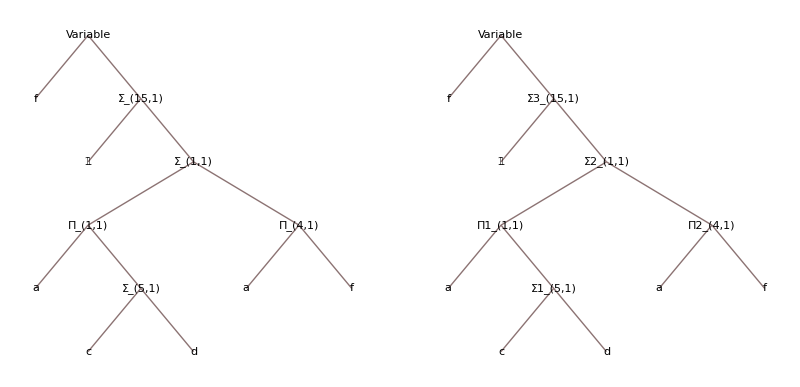

```mathematica
TableForm[ subby@shortDevName@shortName@exprPart2DevsWArgs[analogTestEq]/.Rule->List,TableHeadings-> {None,{"Analog primtives","Physical devices"}}]
GraphicsGrid[{TreeForm@subby@shortDevName@shortName@#@Mathematica2AnalogParadigm@testEquation&/@{Identity,uniqueAnalogExpr}}]
```

#### Identify the wiring

```mathematica
allSubtrees[aexpr_,partList_:ComputationalParts]:= (*was: ElementaryParts *)Flatten[Cases[indent@uniqueAnalogExpr@aexpr,#[_][__],Infinity, Heads->True]&/@devName/@partList];
multiplierMapping:=Head@#-> Multiplicities@#&
multiplierList[aexpr_]:=multiplierMapping/@allSubtrees[aexpr,ComputationalParts]
unMultipliedMapping:=Apply[Head@#,Children@#]& (*removing/hiding the multipliticies *)
edgeList[aexpr_]:=Module[{n=unMultipliedMapping[aexpr]},MapIndexed[{
If[LeafCount@#>1,(Head@#)[outJack],#],(Head@n)[inJack[First@#2]] }&,List@@n]];
wiring[aexpr_]:=Flatten[edgeList/@allSubtrees@aexpr, 1];
wiringWithoutJacks[aexpr_]:=wiring@aexpr//.{x_[inJack[_]]-> x,x_[outJack]-> x};
```

This code is not great but simple enough to demonstrate how to identify variables across the tree (which share a single value and therefore can/should be wired together). Interestingly, the tree is now no more a tree:

```mathematica
wiringWithoutJacks[analogTestEq]//TableForm;
wiring[analogTestEq]//TableForm
TreePlot[shortDevName@shortName@wiringWithoutJacks@analogTestEq/.{a_,b_}->(a->b),
(*Automatic, OutputVariableDev[1],*)(* optional line to define "root" element *) 
PlotTheme->"ClassicLabeled"]
```

c | SummerDev[1][inJack[1]]
d | SummerDev[1][inJack[2]]
MultiplierDev[1][outJack] | SummerDev[2][inJack[1]]
MultiplierDev[2][outJack] | SummerDev[2][inJack[2]]
PlusOne | SummerDev[3][inJack[1]]
SummerDev[2][outJack] | SummerDev[3][inJack[2]]
a | MultiplierDev[1][inJack[1]]
SummerDev[1][outJack] | MultiplierDev[1][inJack[2]]
a | MultiplierDev[2][inJack[1]]
f | MultiplierDev[2][inJack[2]]

-Graphics-

#### Print a wiring list

```mathematica
ComputationalParts2Module = {
Summer -> "SUM", Multiplier-> "MLT",
Integrator->"INT", Divider-> "MSD"(*missing mode*) };
 (* beautifying: Write device addresses more compact/OOP-like *)
IObeautify[naming_]:=naming/.OutputVariableDev[n_][inout_]:> OutputVariableDev[n]; 
beautify[naming_]:=IObeautify@naming \
/.Map[(devName@#)[n_]:> Symbol[ToString[#/.ComputationalParts2Module]<>ToString@n]&,ElementaryParts] \
/. {x_[outJack]:> ToString@x<>".output",x_[inJack[n_]]:> StringForm["``.input(``)",x,n]}
comment="# "<>#&/@#&;
List2String=StringJoin@Riffle[Flatten@#,"\n"]&;
Equation2Wiring[analogEquations_,mmaEquations_:None]:=List2String@{
comment@{
"YAML circuit description for an AnalogParadigm Model-1 CBS module",
"Generated by Svens Mathematica Synthese script, implementing the equation(s):"
},
comment@{ToString@If[mmaEquations~SameQ~None,analogEquations,mmaEquations]},
 {"Parts:"},
(*
Print["  Basic arithmetic units: ", StringForm@@({"`` x ``"}~Join~#)&/@  Transpose@{Length/@exprParts[analogEquations],AnalogParadigmParts}];
Print["  Model-1 modules: ",StringForm@@({"`` x ``"}~Join~#)&/@ ({Ceiling[Last@#*First@#/.AnalogParadigmCounter],First@#/.AnalogParadigmDev2Module}&/@Transpose@{AnalogParadigmParts,Length/@exprParts[analogEquations]})];
*)
 {"Netlist: # Mapping outputs to inputs"},
Map[ToString@StringForm["    ``: ``", beautify@First@#, beautify@Last@#]&,wiring[analogEquations]]
}
Equation2Wiring[analogTestEq,testEquation]
```

# YAML circuit description for an AnalogParadigm Model-1 CBS module
# Generated by Svens Mathematica Synthese script, implementing the equation(s):
# f == 15 + a (5 c + d) + 4 a f
Parts:
Netlist: # Mapping outputs to inputs
    c: SUM1.input(1)
    d: SUM1.input(2)
    MLT1.output: SUM2.input(1)
    MLT2.output: SUM2.input(2)
    PlusOne: SUM3.input(1)
    SUM2.output: SUM3.input(2)
    a: MLT1.input(1)
    SUM1.output: MLT1.input(2)
    a: MLT2.input(1)
    f: MLT2.input(2)

This is fine so far, but we notice that all variables introduced haven’t been made use of anywhere. Loops have not been resolved, etc. Let’s test it with something more realistic:

## Transforming an actual Differential Equation

```mathematica
lorentz={ 
D[x[t],t]==σ(y[t]-x[t]),
D[y[t],t]==x[t](ρ-z[t])-y[t],
D[z[t],t]==x [t]y[t] - β z[t]
};
params = { σ-> 10, β->2.6667,ρ->28};
lorentz//TableForm//TraditionalForm
```

x'(t)==σ (y(t)-x(t))
y'(t)==x(t) (ρ-z(t))-y(t)
z'(t)==x(t) y(t)-β z(t)

```mathematica
IntegrateEquation[x_==y_]:=Integrate[x,t]==Integrate[y,t]
integralLorentz=IntegrateEquation/@lorentz/.params//N;
integralLorentz//TableForm//TraditionalForm
```

x(t)==10. ∫(y(t)-x(t))ⅆt
y(t)==∫(x(t) (28-z(t))-y(t))ⅆt
z(t)==∫(x(t) y(t)-2.6667 z(t))ⅆt

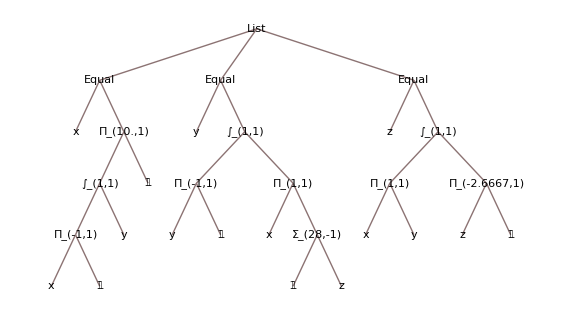

```mathematica
analogLorentz=IntegralEquations2AnalogParadigm[integralLorentz,{x,y,z}];
TreeForm@shortName@subby@analogLorentz
```

```mathematica
wiringWithoutJacks[analogLorentz]
```

{{PlusOne,SummerDev[1]},{z,SummerDev[1]},{x,MultiplierDev[1]},{PlusOne,MultiplierDev[1]},{IntegratorDev[1],MultiplierDev[2]},{PlusOne,MultiplierDev[2]},{y,MultiplierDev[3]},{PlusOne,MultiplierDev[3]},{x,MultiplierDev[4]},{SummerDev[1],MultiplierDev[4]},{x,MultiplierDev[5]},{y,MultiplierDev[5]},{z,MultiplierDev[6]},{PlusOne,MultiplierDev[6]},{MultiplierDev[1],IntegratorDev[1]},{y,IntegratorDev[1]},{MultiplierDev[3],IntegratorDev[2]},{MultiplierDev[4],IntegratorDev[2]},{MultiplierDev[5],IntegratorDev[3]},{MultiplierDev[6],IntegratorDev[3]}}

#### Wiring the Lorentz attractor ODE (naively...)

```mathematica
Graph[shortDevName@shortName@wiringWithoutJacks[analogLorentz]/.{a_,b_}->(a->b), PlotTheme->"ClassicLabeled",GraphLayout->"GravityEmbedding"]
```

-Graphics-

It’s hard to tell something from these graphs, the layouting (and labeling) is not fine-tuned. The previous one shows the wiring (ignoring the jacks at the devices), while the next ones compares how the jack-aware connection graph looks like (i.e. the actual “isovoltage” lines, if you want).

```mathematica
GraphicsGrid[{{
Graph[wiringWithoutJacks[analogLorentz]/.{a_,b_}->(a->b), PlotTheme->"LargeGraph",GraphLayout->"SpringEmbedding"],
Graph[wiring[analogLorentz]/.{a_,b_}->(a->b), PlotTheme->"LargeGraph",GraphLayout->"SpringEmbedding"]
}},ImageSize->Large]
```

-Graphics-

```mathematica
Equation2Wiring[analogLorentz,TableForm@integralLorentz]
```

# YAML circuit description for an AnalogParadigm Model-1 CBS module
# Generated by Svens Mathematica Synthese script, implementing the equation(s):
# x[t] == 10. Integrate[-x[t] + y[t], t]

y[t] == Integrate[-y[t] + x[t] (28 - z[t]), t]

z[t] == Integrate[x[t] y[t] - 2.6667 z[t], t]
Parts:
Netlist: # Mapping outputs to inputs
    PlusOne: SUM1.input(1)
    z: SUM1.input(2)
    x: MLT1.input(1)
    PlusOne: MLT1.input(2)
    INT1.output: MLT2.input(1)
    PlusOne: MLT2.input(2)
    y: MLT3.input(1)
    PlusOne: MLT3.input(2)
    x: MLT4.input(1)
    SUM1.output: MLT4.input(2)
    x: MLT5.input(1)
    y: MLT5.input(2)
    z: MLT6.input(1)
    PlusOne: MLT6.input(2)
    MLT1.output: INT1.input(1)
    y: INT1.input(2)
    MLT3.output: INT2.input(1)
    MLT4.output: INT2.input(2)
    MLT5.output: INT3.input(1)
    MLT6.output: INT3.input(2)

- continued -

-1 -> MultiplierDev1.input(1)

x -> MultiplierDev1.input(2)

10. -> MultiplierDev2.input(1)

IntegratorDev1.output -> MultiplierDev2.input(2)

-1 -> MultiplierDev3.input(1)

y -> MultiplierDev3.input(2)

-1 -> MultiplierDev4.input(1)

z -> MultiplierDev4.input(2)

x -> MultiplierDev5.input(1)

AdderDev2.output -> MultiplierDev5.input(2)

x -> MultiplierDev6.input(1)

y -> MultiplierDev6.input(2)

-2.6667 -> MultiplierDev7.input(1)

z -> MultiplierDev7.input(2)

AdderDev1.output -> IntegratorDev1.input(1)

AdderDev3.output -> IntegratorDev2.input(1)

AdderDev4.output -> IntegratorDev3.input(1)

#### Review of the Lorentz attractor wiring

The generated circuit differs a lot from the one proposed by Bernd in his books. An obvious reasons (telling from the equations itself) is that no efforts have been made to check any bounds (scaling of voltages/logic levels, probably introducing helper quantities). Furthermore, as said in the introductory example above, there is a number of general shortcomings, such as that we don’t enumerate Model-1 modules, i.e. don’t take them into account at the wiring output.